0

1.7×10^-11

0.00729753

0.1101

0.09207

5.×10^-8

1.31×10^-6

0.000022

0.000256

5.×10^-7

0.134977

1.8×10^-7

0.13957

0.000017

0.547862

0.00023

0.77526

0.00013

0.78266

0.000016

1.01946

0.00013

0.00868

0.0008

0.1491

0.000013

0.004249

49/50

0.000016

0.493677

-Graphics3D-

0.01

0.7

0.01

0.65

0.5

0.722566

0.1

0.0575959

0.02

0.83

0.233333

0.435815

0.698839

0.133483

0.0402948

0.208628

0.10169

0.0932834

0.00840662

21.186

28.9353

3.81927×10^-7

2.99184×10^-8

6.23344×10^-10

1.58×10^-10

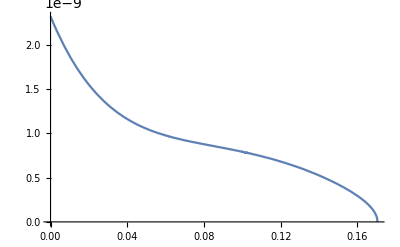

0.0055

3.68×10^-9

1.16×10^-9

0.0375

2.02×10^-9

5.7×10^-10

0.0575

2.22×10^-9

4.8×10^-10

0.0775

2.01×10^-9

4.4×10^-10

0.0975

1.97×10^-9

4.1×10^-10

0.11875

1.77×10^-9

3.6×10^-10

0.15

9.5×10^-10

2.3×10^-10

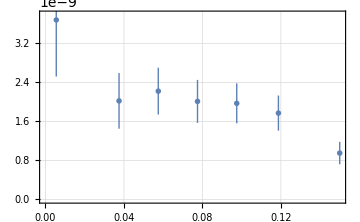

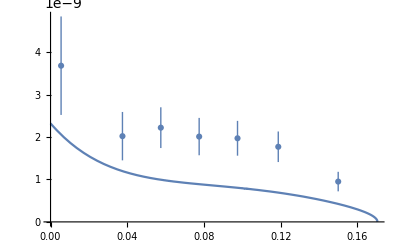

1.58×10^-10

0.000120611

```mathematica
VarianceInput = 0
Δα=0.000000017*10^(-3)
α=7.297525664*10^(-3)+VarianceInput*RandomReal[{-1,1}]*Δα
fK =110.10*10^(-3)
fπ =92.07*10^(-3)
ΔΓtotal=0.05*10^(-6)
Γtotal=1.31*10^(-6)+VarianceInput*RandomReal[{-1,1}]*ΔΓtotal
ΔBR=0.22*10^(-4)
BR=2.56*10^(-4)+VarianceInput*RandomReal[{-1,1}]*ΔBR
Δmπ=0.0005*10^(-3)
mπ=134.9768*10^(-3)+VarianceInput*RandomReal[{-1,1}]*Δmπ
ΔmπA=0.00018*10^(-3)
mπA=139.57039*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔmπA
ΔMη=0.017*10^(-3)
Mη = 547.862*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔMη
Δmρ=0.23*10^(-3)
mρ=775.26*10^(-3)+VarianceInput*RandomReal[{-1,1}]*Δmρ
Δmω=0.13*10^(-3)
mω=782.66*10^(-3)+VarianceInput*RandomReal[{-1,1}]*Δmω
Δmϕ=0.016*10^(-3)
mϕ=1019.461*10^(-3)+VarianceInput*RandomReal[{-1,1}]*Δmϕ
ΔΓω =0.13*10^(-3)
Γω = 8.68*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔΓω
ΔΓρ=0.8*10^(-3)
Γρ = 149.1*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔΓρ
ΔΓϕ=0.013*10^(-3)
Γϕ = 4.249*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔΓϕ
maZero = 980*10^(-3)
ΔmKP=0.016*10^(-3)
mKP=493.677*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔmKP
ΓρEff[t_] :=Γρ*((-4 mπA^2+t)/(-4 mπA^2+mρ^2))^(3/2) *HeavisideTheta[-4 mπA^2+t]
m232MAX[m132_] := ((Mη^2+mπ^2)^2)/(4 m132)-(-(-m132+Mη^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
m232MIN[m132_] := ((Mη^2+mπ^2)^2)/(4 m132)-((-m132+Mη^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
Constraint[m132_, m232_]:=HeavisideTheta[m232MAX[m132]-m232]*HeavisideTheta[m232-m232MIN[m132]]
Plot3D[Constraint[m132, m232], {m132, mπ^2, Mη^2},{m232, mπ^2, Mη^2}, PlotRange->All]
Δg=0.01
g = 0.70+VarianceInput*RandomReal[{-1,1}]*Δg
ΔzSmBm=0.01
zSmBm = 0.65+VarianceInput*RandomReal[{-1,1}]*ΔzSmBm
ΔϕP=0.5
ϕP = (41.4 +VarianceInput*RandomReal[{-1,1}]*ΔϕP)Degree
ΔϕV=0.1
ϕV =(3.3 +VarianceInput*RandomReal[{-1,1}]*ΔϕV)Degree
ΔzNS=0.02
zNS = 0.83+VarianceInput*RandomReal[{-1,1}]*ΔzNS
gρπγ = g/3
gρηγ = g*zNS*Cos[ϕP]
gωπγ = g*Cos[ϕV]
gωηγ =g/3*(zNS*Cos[ϕP]*Cos[ϕV]-2*zSmBm*Sin[ϕP]*Sin[ϕV])
gϕπγ = g*Sin[ϕV]
gϕηγ =g/3*(zNS*Cos[ϕP]*Sin[ϕV]+2*zSmBm*Sin[ϕP]*Cos[ϕV])
cρ = gρπγ*gρηγ
cω = gωπγ*gωηγ
cϕ = gϕπγ*gϕηγ
Bq2Bq2p[m132_,m232_]:=1/8 (m132^2+Mη^4) (-m132-m232+Mη^2+mπ^2)^2 +1/8 (-m132+Mη^2) (-m232+Mη^2) (m132 m232+Mη^2 (m132+m232-Mη^2-2 mπ^2))
Bq1Bq1[m132_,m232_]:=1/8 (m232^2+Mη^4) (-m132-m232+Mη^2+mπ^2)^2 +1/8 (-m132+Mη^2) (-m232+Mη^2) (m132 m232+Mη^2 (m132+m232-Mη^2-2 mπ^2))
Bq2Bq1[m132_,m232_]:=1/8 (m132*m232+Mη^4) (-m132-m232+Mη^2+mπ^2)^2 +1/8 (-m132+Mη^2) (-m232+Mη^2) (m132 m232+Mη^2 (m132+m232-Mη^2-2 mπ^2))
BWt[m132_,m232_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)]^2
BWu[m132_,m232_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)]^2
BWtu[m132_,m232_] :=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω))]
MatrixVMD[m132_,m232_] := (Bq2Bq2p[m132,m232]*BWt[m132,m232]+2*Bq2Bq1[m132,m232]*BWtu[m132,m232] +Bq2Bq1[m132,m232]*BWu[m132,m232])*Constraint[m132, m232]
βPlusπη[s_]:=√(1-(Mη+mπ)^2/s)
βMinusπη[s_]:=√(1-(Mη-mπ)^2/s)
βBarPlusπη[s_]:=√(-1+(Mη+mπ)^2/s)
βBarMinusπη[s_]:=√(-1+(-Mη+mπ)^2/s)
βK[s_]:=√(1-(4*mKP^2)/s)
βKbar[s_]:=√((4*mKP^2)/s-1)
θπη[s_]:= HeavisideTheta[-(Mη+mπ)^2+s]
Barθπη[s_]:= HeavisideTheta[(Mη+mπ)^2-s]*HeavisideTheta[-(-Mη+mπ)^2+s]
BarBarθπη[s_]:= HeavisideTheta[(-Mη+mπ)^2-s]
θK[s_]:= HeavisideTheta[-4*mKP^2+s]
θKbar[s_]:= HeavisideTheta[4*mKP^2-s]
ga0KKbarSq=((-maZero^2+mKP^2)^2)/(2 fK^2)
ga0πηSq=((-maZero^2+Mη^2)^2 Cos[ϕP]^2)/fπ^2
R1[s_]:=ga0KKbarSq/(16 π^2)*(2-Log[(1+βK[s])/(1-βK[s])] *βK[s]* θK[s]-2 ArcTan[1/βKbar[s]]* βKbar[s]* θKbar[s])
R2[s_]:=ga0πηSq/(16 π^2)*(2-((Mη^2-mπ^2) *Log[Mη/mπ])/s-Log[(βMinusπη[s]+βPlusπη[s])/(βMinusπη[s]-βPlusπη[s])]* βMinusπη[s]* βPlusπη[s]* θπη[s])
R3[s_]:=ga0πηSq/(16 π^2)*(BarBarθπη[s]*Log[(βBarMinusπη[s]+βBarPlusπη[s])/(-βBarMinusπη[s]+βBarPlusπη[s])]*βBarMinusπη[s]*βBarPlusπη[s]-2*ArcTan[βMinusπη[s]/βBarPlusπη[s]]*Barθπη[s]*βBarPlusπη[s]*βMinusπη[s])
R[s_]:=R1[s]+R2[s]+R3[s]
ImaginaryPart[s_]:=-(ga0KKbarSq* βK[s]* θK[s])/(16 π)-(ga0πηSq* βPlusπη[s]* βMinusπη[s]*θπη[s])/(16 π)
Da0[s_]:=-maZero^2+s+R[s]-R[maZero^2]+I*ImaginaryPart[s]
ALSM[s_]:=1/(2*fK*fπ)*((-Mη^2+s)*((-maZero^2+mKP^2)/Da0[s])*Cos[ϕP]+1/6 ((5 Mη^2+mπ^2-3 s)*Cos[ϕP]-√2*(4 mKP^2+Mη^2+mπ^2-3 s)*Sin[ϕP]))
f[z_]:=1/4* HeavisideTheta[1/4-z] *(-ⅈ π+Log[(1+√(1-4 z))/(1-√(1-4 z))])^2-ArcSin[1/(2 √z)]^2 HeavisideTheta[-1/4+z]
L[z_]:=-1/(2 z)-(2 f[1/z])/z^2
Int1VMDLSM[m132_,m232_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+Mη^2+mπ^2)/mKP^2]*ALSM[-m132-m232+Mη^2+mπ^2]
Int2VMDLSM[m132_,m232_]:=-Conjugate[1/4 (-m132-m232+Mη^2+mπ^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)))]
Interference[m132_,m232_]:=2*Re[Int1VMDLSM[m132,m232]*Int2VMDLSM[m132,m232]]*Constraint[m132, m232]
LSM[m132_,m232_]:=((-m132-m232+Mη^2+mπ^2)^2*Abs[(α ALSM[-m132-m232+Mη^2+mπ^2]* L[(-m132-m232+Mη^2+mπ^2)/mKP^2])/mKP^2]^2)/π^2*Constraint[m132, m232]
Integrand1 = NIntegrate[MatrixVMD[m132,m232], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand2 = NIntegrate[Interference[m132,m232], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand3 = NIntegrate[LSM[m132,m232], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Width = (1/2)*1/(256 Mη^3 π^3)*(Integrand1+Integrand2+Integrand3)
γγSpectrum[m122_] := NIntegrate[(1/2)*1/(256 Mη^3 π^3)*(MatrixVMD[m132,Mη^2+mπ^2 - m132 - m122]+Interference[m132,Mη^2+mπ^2 - m132 - m122]+LSM[m132,Mη^2+mπ^2 - m132 - m122])*Constraint[m132, Mη^2+mπ^2 - m132 - m122], {m132, mπ^2,Mη^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
pTheory= Plot[γγSpectrum[m122],{m122, 0, (Mη-mπ)^2} , MaxRecursion->5]
p1 = 0.0055
v1 = 3.68*10^(-9)
u1 = (1.16)*10^(-9)
p2 = 0.0375
v2 = 2.02*10^(-9)
u2 = (0.57)*10^(-9)
p3 = 0.0575
v3 = 2.22*10^(-9)
u3 = (0.48)*10^(-9)
p4 = 0.0775
v4 = 2.01*10^(-9)
u4 = (0.44)*10^(-9)
p5 =0.0975
v5=1.97*10^(-9)
u5 = (0.41)*10^(-9)
p6 = 0.11875
v6 =1.77*10^(-9)
u6=(0.36)*10^(-9)
p7 =0.15
v7 =0.95*10^(-9)
u7  = (0.23)*10^(-9)
pExp=ListPlot[{{Around[p1,0],Around[v1,u1]},
{Around[p2,0],Around[v2,u2]},
{Around[p3,0],Around[v3,u3]},
{Around[p4,0],Around[v4, u4]},
{Around[p5,0],Around[v5,u5]},
{Around[p6,0],Around[v6,u6]},
{Around[p7,0],Around[v7,u7]}},Sequence[PlotTheme->"Detailed",ImageSize->Medium]]
Show[pTheory, pExp, PlotRange->All]
Width
BranchingTheory=Width/Γtotal
```

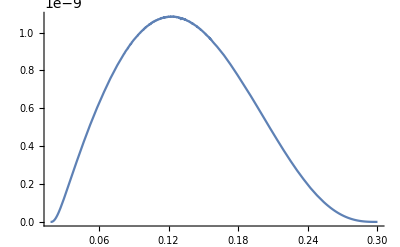

```mathematica
πγ1[m132_] := NIntegrate[MatrixVMD[m132,m232], {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγ2[m132_] := NIntegrate[Interference[m132,m232],  {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγ3[m132_] := NIntegrate[LSM[m132,m232],  {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrum[m132_]  := (1/2)*1/(256 Mη^3 π^3)*(πγ1[m132]+πγ2[m132]+πγ3[m132])
πγSpectrumPlot= Plot[πγSpectrum[m132],{m132, (mπ)^2, (Mη)^2} , MaxRecursion->5, PlotRange->All]
```

```mathematica
(*Result 1*)
(*1.5010009888626408*^-10*)
(* 0.00011701682409837921*)
(*Result 2*)
(*1.520250829295853*^-10*)
(*0.00011379350744141524*)
(*Result 3*)
(*1.5475948234164414*^-10*)
(*0.0001166518575543098*)
(*Result 4*)
(*1.6954631110267764*^-10*)
(*0.0001267490854545344*)
(*Result 5*)
(*1.5705159529356582*^-10*)
(*0.00011973475231538188*)
(*Result 6*)
(*1.4851983095575572*^-10*)
(*0.00011643397457207366*)
(*Result 7*)
(*1.560663247200986*^-10*)
(*0.00011700346580924131*)
(*Result 8*)
(*1.502780341961886*^-10*)
(*0.0001188293405542128*)
(*Result 9*)
(*1.5853018589199106*^-10*)
(*0.00011818982272286403*)
(*Result 10*)
(*1.67880628190278*^-10*)
(*0.00012908515683143177*)
```

```mathematica
Mean[{1.5010009888626408*^-10,1.520250829295853*^-10,1.5475948234164414*^-10,1.6954631110267764*^-10,1.5705159529356582*^-10,1.4851983095575572*^-10,1.560663247200986*^-10,1.502780341961886*^-10,1.5853018589199106*^-10,1.67880628190278*^-10}]
```

1.56476×10^-10

```mathematica
(Variance[{1.5010009888626408*^-10,1.520250829295853*^-10,1.5475948234164414*^-10,1.6954631110267764*^-10,1.5705159529356582*^-10,1.4851983095575572*^-10,1.560663247200986*^-10,1.502780341961886*^-10,1.5853018589199106*^-10,1.67880628190278*^-10}])^(1/2)
```

7.2322×10^-12

```mathematica
Mean[{0.00011701682409837921,0.00011379350744141524,0.0001166518575543098,0.0001267490854545344,0.00011973475231538188,0.00011643397457207366,0.00011700346580924131,0.0001188293405542128,0.00011818982272286403,0.00012908515683143177}]
```

0.000119349

```mathematica
EngineeringForm[Mean[{0.00011701682409837921,0.00011379350744141524,0.0001166518575543098,0.0001267490854545344,0.00011973475231538188,0.00011643397457207366,0.00011700346580924131,0.0001188293405542128,0.00011818982272286403,0.00012908515683143177}]]
```

119.349×10^-6

```mathematica
EngineeringForm[(Variance[{0.00011701682409837921,0.00011379350744141524,0.0001166518575543098,0.0001267490854545344,0.00011973475231538188,0.00011643397457207366,0.00011700346580924131,0.0001188293405542128,0.00011818982272286403,0.00012908515683143177}])^(1/2)]
```

4.81771×10^-6

```mathematica
(*VMD-LσM interference is around 7-8%*)
```

```mathematica
Integrand2/Integrand1
```

0.0747284

```mathematica
EngineeringForm[BranchingTheory]
```

129.085×10^-6

```mathematica
(*Minimize χ^2 = ∑_(i=1)^N (Subscript[Theory, i]- Subscript[Experiment, i])^2/Subscript[σ, i]^2*)
```

```mathematica
BWtDARK[m132_,m232_,cB_,ΓB_,mB_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+cB/(- m132+mB^2-ⅈ mB* ΓB)]^2
BWuDARK[m132_,m232_,cB_,ΓB_,mB_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+cB/(-m232+mB^2-ⅈ* mB* ΓB)]^2
BWtuDARK[m132_,m232_,cB_,ΓB_,mB_]:=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+cB/(-m132+mB^2-ⅈ *mB* ΓB))*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω)+cB/(-m232+mB^2+ⅈ *mB* ΓB))]
MatrixVMDDARK[m132_,m232_,cB_,ΓB_,mB_] := (Bq2Bq2p[m132,m232]*BWtDARK[m132,m232,cB,ΓB,mB]+2*Bq2Bq1[m132,m232]*BWtuDARK[m132,m232,cB,ΓB,mB] +Bq2Bq1[m132,m232]*BWuDARK[m132,m232,cB,ΓB,mB])*Constraint[m132, m232]
Int1VMDLSMDARK[m132_,m232_,cB_,ΓB_,mB_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+Mη^2+mπ^2)/mKP^2]*ALSM[-m132-m232+Mη^2+mπ^2]
Int2VMDLSMDARK[m132_,m232_,cB_,ΓB_,mB_]:=-Conjugate[1/4 (-m132-m232+Mη^2+mπ^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+cB/(-m132+mB^2-ⅈ *mB* ΓB))+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+cB/(-m232+mB^2-ⅈ *mB* ΓB)))]
InterferenceDARK[m132_,m232_,cB_,ΓB_,mB_]:=2*Re[Int1VMDLSMDARK[m132,m232,cB,ΓB,mB]*Int2VMDLSMDARK[m132,m232,cB,ΓB,mB]]*Constraint[m132, m232]
γγSpectrumDARK[m122_,cB_,ΓB_,mB_] := NIntegrate[(1/2)*1/(256 Mη^3 π^3)*(MatrixVMDDARK[m132,Mη^2+mπ^2 - m132 - m122,cB,ΓB,mB]+InterferenceDARK[m132,Mη^2+mπ^2 - m132 - m122,cB,ΓB,mB]+LSM[m132,Mη^2+mπ^2 - m132 - m122])*Constraint[m132, Mη^2+mπ^2 - m132 - m122], {m132, mπ^2,Mη^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->50]
Loss[x_,Γ_,mB_]:=(γγSpectrumDARK[p1,x, Γ,mB]- v1)^2/u1^2+(γγSpectrumDARK[p2,x, Γ,mB]- v2)^2/u2^2+(γγSpectrumDARK[p3,x, Γ,mB]- v3)^2/u3^2+(γγSpectrumDARK[p4,x, Γ,mB]- v4)^2/u4^2+(γγSpectrumDARK[p5,x, Γ,mB]- v5)^2/u5^2+(γγSpectrumDARK[p6,x, Γ,mB]- v6)^2/u6^2+(γγSpectrumDARK[p7,x, Γ,mB]- v7)^2/u7^2
```

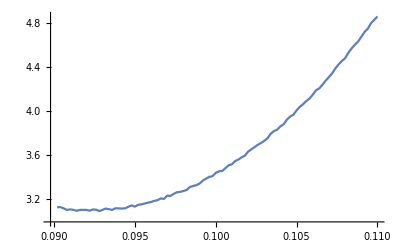

```mathematica
ListPlot[Table[{0.09 + (0.02/100)*k,Loss[0.09 + (0.02/100)*k,Γω/2,mω-Γω/2]},{k, 1, 100}],Joined->True]
```

```mathematica
(*Result 1 = 0.10*)
(*Result 2 = 0.10*)
(*Result 3 = 0.10*)
(*Result 4 = 0.09*)
(*Result 5 = 0.10*)
(*Result 6 = 0.10*)
(*Result 7 = 0.10*)
(*Result 8 = 0.10*)
(*Result 9 = 0.10*)
(*Result 10 = 0.09*)
Mean[{0.10,0.10,0.10,0.09,0.10,0.10,0.10,0.10,0.10,0.09 }]
```

0.098

```mathematica
(Variance[{0.10,0.10,0.10,0.09,0.10,0.10,0.10,0.10,0.10,0.09 }])^(1/2)
```

0.00421637

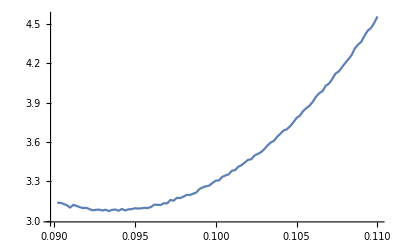

```mathematica
ListPlot[Table[{0.09 + (0.02/100)*k,Loss[0.09 + (0.02/100)*k,Γω/2,mω]},{k, 1, 100}],Joined->True]
```

```mathematica
(*Result 1 = 0.11*)
(*Result 2 = 0.10*)
(*Result 3 = 0.10*)
(*Result 4 = 0.09*)
(*Result 5 = 0.10*)
(*Result 6 = 0.11*)
(*Result 7 = 0.10*)
(*Result 8 = 0.11*)
(*Result 9 = 0.10*)
(*Result 10 = 0.09*)
Mean[{0.11,0.10,0.10,0.09,0.10,0.11,0.10,0.11,0.10,0.09}]
```

0.101

```mathematica
(Variance[{0.11,0.10,0.10,0.09,0.10,0.11,0.10,0.11,0.10,0.09}])^(1/2)
```

0.00737865

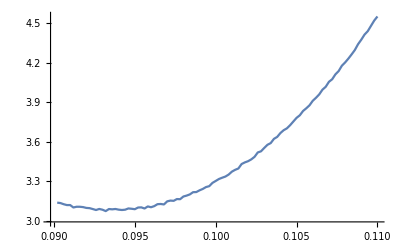

```mathematica
ListPlot[Table[{0.09 + (0.02/100)*k,Loss[0.09 + (0.02/100)*k,Γω,mω]},{k, 1, 100}],Joined->True]
```

```mathematica
(*Result 1 = 0.11*)
(*Result 2 = 0.10*)
(*Result 3 = 0.10*)
(*Result 4 = 0.09*)
(*Result 5 = 0.10*)
(*Result 6 = 0.11*)
(*Result 7 = 0.10*)
(*Result 8 = 0.11*)
(*Result 9 = 0.10*)
(*Result 10 = 0.09*)

Mean[{0.11,0.10,0.10,0.09,0.10,0.11,0.10,0.11,0.10,0.09}]
```

0.101

```mathematica
(Variance[{0.11,0.10,0.10,0.09,0.10,0.11,0.10,0.11,0.10,0.09}])^(1/2)
```

0.00737865

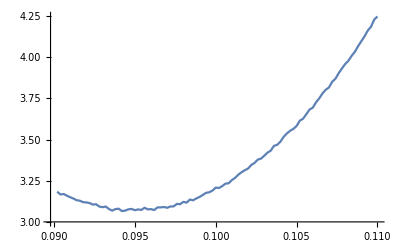

```mathematica
ListPlot[Table[{0.09 + (0.02/100)*k,Loss[0.09 + (0.02/100)*k,Γω/2,mω+Γω/2]},{k, 1, 100}],Joined->True]
```

```mathematica
(*Result 1 = 0.11*)
(*Result 2 = 0.11*)
(*Result 3 = 0.10*)
(*Result 4 = 0.09*)
(*Result 5 = 0.10*)
(*Result 6 = 0.11*)
(*Result 7 = 0.10*)
(*Result 8 = 0.11*)
(*Result 9 = 0.10*)
(*Result 10 = 0.09*)
Mean[{0.11,0.11,0.10,0.09,0.10,0.11,0.10,0.11,0.10,0.09}]
```

0.102

```mathematica
(Variance[{0.11,0.11,0.10,0.09,0.10,0.11,0.10,0.11,0.10,0.09}])^(1/2)
```

0.00788811

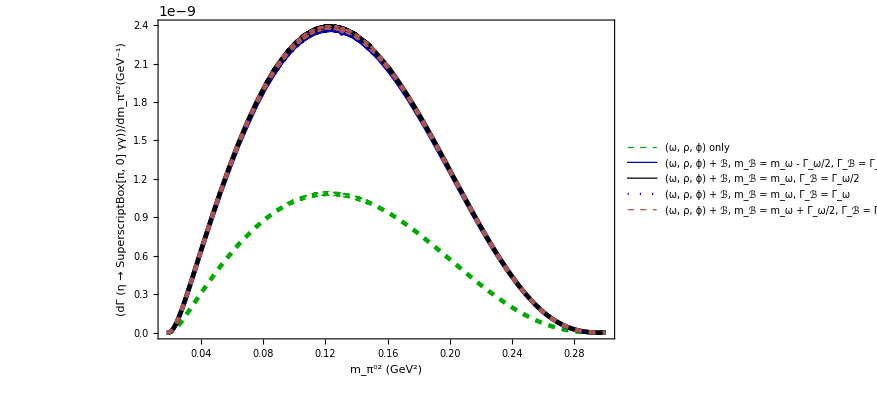

```mathematica
πγ1Dark[m132_,cB_,ΓB_,mB_]:= NIntegrate[MatrixVMDDARK[m132,m232,cB,ΓB,mB], {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγ2Dark[m132_,cB_,ΓB_,mB_] := NIntegrate[InterferenceDARK[m132,m232,cB,ΓB,mB],  {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγ3Dark[m132_,cB_,ΓB_,mB_] := NIntegrate[LSM[m132,m232],  {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrumDark[m132_,cB_,ΓB_,mB_]  := (1/2)*1/(256 Mη^3 π^3)*(πγ1Dark[m132,cB,ΓB,mB]+πγ2Dark[m132,cB,ΓB,mB]+πγ3Dark[m132,cB,ΓB,mB])
πγSpectrumPlotOverall = Plot[{{πγSpectrum[m132]},{πγSpectrumDark[m132,0.098,Γω/2,mω-Γω/2]},{πγSpectrumDark[m132,0.101,Γω/2,mω]},{πγSpectrumDark[m132,0.101,Γω,mω]},{πγSpectrumDark[m132,0.102,Γω/2,mω+Γω/2]}},{m132, (mπ)^2, (Mη)^2}, PlotRange->All,PlotStyle->{Directive[Darker[Green], Thickness[0.005], Dashed],Directive[Darker[Blue], Thickness[0.005]],Directive[Darker[Black],Thickness[0.005]],Directive[Darker[Blue],Dotted],Directive[Darker[Pink], Dashed,Thickness[0.005]],Directive[Darker[Red], Thickness[0.005]]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"(ω, ρ, ϕ) only","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω - Γ_ω/2, Γ_ℬ = Γ_ω/2","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω, Γ_ℬ = Γ_ω/2","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω, Γ_ℬ = Γ_ω","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω + Γ_ω/2, Γ_ℬ = Γ_ω/2"}, LegendFunction->Framed], Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"m_(π^0)^2 (GeV^2)","(dΓ (η →  SuperscriptBox[π, 0] γγ))/(dm_(π^0)^2)(GeV^-1)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650,Axes->False]
```

```mathematica
Export["EtaPiPi0Gamma.png",πγSpectrumPlotOverall]
```

EtaPiPi0Gamma.png

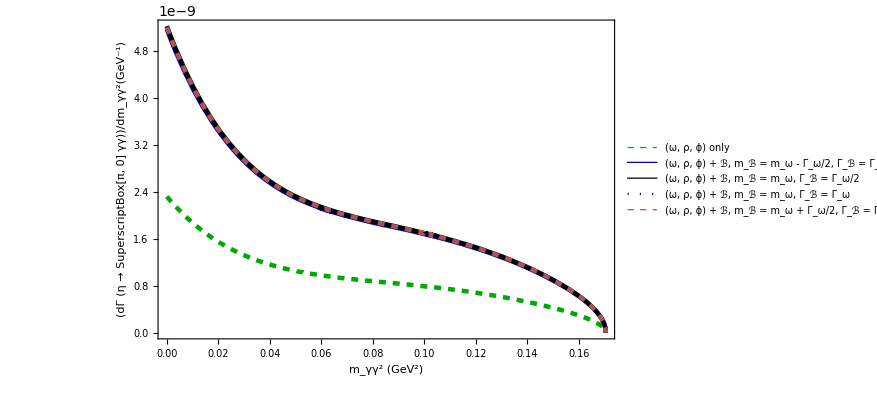

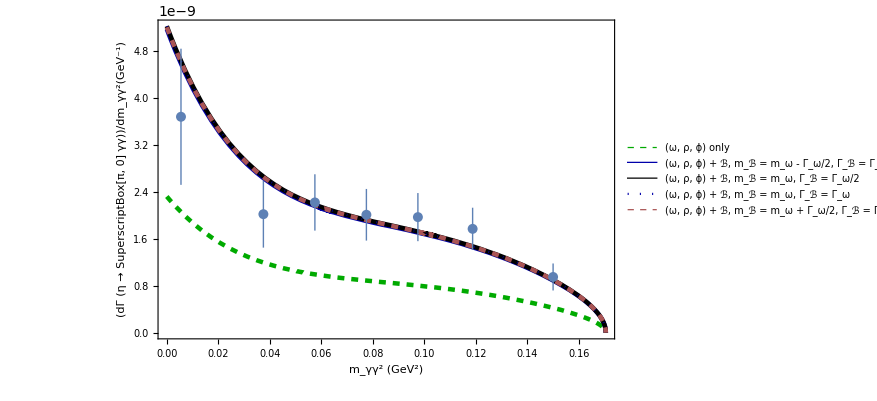

```mathematica
SummaryTheory = Plot[{{γγSpectrum[m122]},{γγSpectrumDARK[m122,0.098,Γω/2,mω-Γω/2]},{γγSpectrumDARK[m122,0.101,Γω/2,mω]},{γγSpectrumDARK[m122,0.101,Γω,mω]},{γγSpectrumDARK[m122,0.102,Γω/2,mω+Γω/2]}},{m122, 0, (Mη-mπ)^2}, PlotRange->All,PlotStyle->{Directive[Darker[Green], Thickness[0.005], Dashed],Directive[Darker[Blue], Thickness[0.005]],Directive[Darker[Black],Thickness[0.005]],Directive[Darker[Blue],Dotted],Directive[Darker[Pink], Dashed,Thickness[0.005]],Directive[Darker[Red], Thickness[0.005]]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"(ω, ρ, ϕ) only","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω - Γ_ω/2, Γ_ℬ = Γ_ω/2","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω, Γ_ℬ = Γ_ω/2","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω, Γ_ℬ = Γ_ω","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω + Γ_ω/2, Γ_ℬ = Γ_ω/2"}, LegendFunction->Framed], Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"m_γγ^2 (GeV^2)","(dΓ (η →  SuperscriptBox[π, 0] γγ))/dm_γγ^2(GeV^-1)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650]
pFinal = Show[SummaryTheory, pExp]
```

```mathematica
Export["EtaPi.png",pFinal]
```

EtaPi.png

```mathematica
Integrand1Dark = NIntegrate[MatrixVMDDARK[m132,m232,0.09,Γω/2,mω-Γω/2], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand2Dark = NIntegrate[InterferenceDARK[m132,m232,0.09,Γω/2,mω-Γω/2], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand3Dark = NIntegrate[LSM[m132,m232], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
WidthDark = (1/2)*1/(256 Mη^3 π^3)*(Integrand1Dark+Integrand2Dark+Integrand3Dark)
BranchingDark=WidthDark/Γtotal
```

8.43638×10^-7

4.37261×10^-8

6.0767×10^-10

3.40135×10^-10

0.000261533

```mathematica
(*Result 1*)
(*3.362233651351122*^-10*)
(*0.00026211701836114493*)
(*Result 2*)
(*3.3808992679279155*^-10*)
(*0.0002530663878551058*)
(*Result 3*)
(*3.432441038192835*^-10*)
(*0.0002587244522871438*)
(*Result 4*)
(*3.4185081527184006*^-10*)
(*0.0002555601352562156*)
(*Result 5*)
(*3.4683495646248053*^-10*)
(*0.0002644239145022726*)
(*Result 6*)
(*3.339453286175821*^-10*)
(*0.00026180060703345076*)
(*Result 7*)
(*3.456455288227484*^-10*)
(*0.0002591316537136431*)
(*Result 8*)
(*3.366439907154328*^-10*)
(*0.0002661944816634285*)
(*Result 9*)
(*3.477099074279169*^-10*)
(*0.0002592299509816264*)
(*Result 10*)
(*3.4013452248227195*^-10*)
(*0.0002615329633425261*)
```

```mathematica
Width=Mean[{3.362233651351122*^-10,3.3808992679279155*^-10,3.432441038192835*^-10,3.4185081527184006*^-10,3.4683495646248053*^-10,3.339453286175821*^-10,3.456455288227484*^-10,3.366439907154328*^-10,3.477099074279169*^-10,3.4013452248227195*^-10}]
```

3.41032×10^-10

```mathematica
ΔWidth = (Variance[{3.362233651351122*^-10,3.3808992679279155*^-10,3.432441038192835*^-10,3.4185081527184006*^-10,3.4683495646248053*^-10,3.339453286175821*^-10,3.456455288227484*^-10,3.366439907154328*^-10,3.477099074279169*^-10,3.4013452248227195*^-10}])^(1/2)
```

4.79788×10^-12

```mathematica
Branching=EngineeringForm[Mean[{0.00026211701836114493,0.0002530663878551058,0.0002587244522871438,0.0002555601352562156,0.0002644239145022726,0.00026180060703345076,0.0002591316537136431,0.0002661944816634285,0.0002592299509816264,0.0002615329633425261}]]
```

260.178×10^-6

```mathematica
ΔBranching=EngineeringForm[(Variance[{0.00026211701836114493,0.0002530663878551058,0.0002587244522871438,0.0002555601352562156,0.0002644239145022726,0.00026180060703345076,0.0002591316537136431,0.0002661944816634285,0.0002592299509816264,0.0002615329633425261}])^(1/2)]
```

3.92231×10^-6

```mathematica
Integrand1Dark = NIntegrate[MatrixVMDDARK[m132,m232,0.09,Γω/2,mω], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand2Dark = NIntegrate[InterferenceDARK[m132,m232,0.09,Γω/2,mω], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand3Dark = NIntegrate[LSM[m132,m232], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
WidthDark = (1/2)*1/(256 Mη^3 π^3)*(Integrand1Dark+Integrand2Dark+Integrand3Dark)
BranchingDark=WidthDark/Γtotal
```

NIntegrate::inumr: The integrand MatrixVMDDARK[m132,m232,0.09,0.00434,0.78266] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate[MatrixVMDDARK[m132,m232,0.09,Γω/2,mω],{m132,mπ^2,Mη^2},{m232,mπ^2,Mη^2},AccuracyGoal→30,Method→{AdaptiveQuasiMonteCarlo},MaxRecursion→100]

NIntegrate::inumr: The integrand InterferenceDARK[m132,m232,0.09,0.00434,0.78266] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate[InterferenceDARK[m132,m232,0.09,Γω/2,mω],{m132,mπ^2,Mη^2},{m232,mπ^2,Mη^2},AccuracyGoal→30,Method→{AdaptiveQuasiMonteCarlo},MaxRecursion→100]

6.24166×10^-10

NIntegrate::inumr: The integrand MatrixVMDDARK[m132,m232,0.09,0.00434,0.78266] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand InterferenceDARK[m132,m232,0.09,0.00434,0.78266] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.00038306 (6.24166×10^-10+NIntegrate[InterferenceDARK[m132,m232,0.09,Γω/2,mω],{m132,mπ^2,Mη^2},{m232,mπ^2,Mη^2},AccuracyGoal→30,Method→{AdaptiveQuasiMonteCarlo},MaxRecursion→100]+NIntegrate[MatrixVMDDARK[m132,m232,0.09,Γω/2,mω],{m132,mπ^2,Mη^2},{m232,mπ^2,Mη^2},AccuracyGoal→30,Method→{AdaptiveQuasiMonteCarlo},MaxRecursion→100])

NIntegrate::inumr: The integrand InterferenceDARK[m132,m232,0.09,0.00434,0.78266] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand MatrixVMDDARK[m132,m232,0.09,0.00434,0.78266] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand InterferenceDARK[m132,m232,0.09,0.00434,0.78266] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

292.412 (6.24166×10^-10+NIntegrate[InterferenceDARK[m132,m232,0.09,Γω/2,mω],{m132,mπ^2,Mη^2},{m232,mπ^2,Mη^2},AccuracyGoal→30,Method→{AdaptiveQuasiMonteCarlo},MaxRecursion→100]+NIntegrate[MatrixVMDDARK[m132,m232,0.09,Γω/2,mω],{m132,mπ^2,Mη^2},{m232,mπ^2,Mη^2},AccuracyGoal→30,Method→{AdaptiveQuasiMonteCarlo},MaxRecursion→100])

```mathematica
(*Result 1*)
(*3.550767400678206*^-10*)
(*0.0002768149571002341*)
(*Result 2*)
(*3.336350926375653*^-10*)
(*0.0002497318644078941*)
(*Result 3*)
(*3.336350926375653*^-10*)
(*0.0002497318644078941*)
(*Result 4*)
(*3.3868962913929453*^-10*)
(*0.00025319690217467104*)
(*Result 5*)
(*3.44473657292939*^-10*)
(*0.00026262368082314897*)
(*Result 6*)
(*3.523480355579673*^-10*)
(*0.00027622763875147395*)
(*Result 7*)
(*3.4162301303842616*^-10*)
(*0.0002561159596561187*)
(*Result 8*)
(*3.539041167348246*^-10*)
(*0.00027984258002815255*)
(*Result 9*)
(*3.445498533515147*^-10*)
(*0.0002568740196554681*)
(*Result 10*)
(*3.356765988463468*^-10*)
(*0.00025810521960646074*)

Width=Mean[{3.550767400678206*^-10,3.336350926375653*^-10,3.336350926375653*^-10,3.3868962913929453*^-10,3.44473657292939*^-10,3.523480355579673*^-10,3.4162301303842616*^-10,3.539041167348246*^-10,3.445498533515147*^-10,3.356765988463468*^-10}]
```

3.43361×10^-10

```mathematica
ΔWidth=(Variance[{3.550767400678206*^-10,3.336350926375653*^-10,3.336350926375653*^-10,3.3868962913929453*^-10,3.44473657292939*^-10,3.523480355579673*^-10,3.4162301303842616*^-10,3.539041167348246*^-10,3.445498533515147*^-10,3.356765988463468*^-10}])^(1/2)
```

8.19833×10^-12

```mathematica
Branching=EngineeringForm[Mean[{0.0002768149571002341,0.0002497318644078941,0.0002497318644078941,0.00025319690217467104,0.00026262368082314897,0.00027622763875147395,0.0002561159596561187,0.00027984258002815255,0.0002568740196554681,0.00025810521960646074}]]
```

261.926×10^-6

```mathematica
ΔBranching=EngineeringForm[(Variance[{0.0002768149571002341,0.0002497318644078941,0.0002497318644078941,0.00025319690217467104,0.00026262368082314897,0.00027622763875147395,0.0002561159596561187,0.00027984258002815255,0.0002568740196554681,0.00025810521960646074}])^(1/2)]
```

11.5238×10^-6

```mathematica
Integrand1Dark = NIntegrate[MatrixVMDDARK[m132,m232,0.09,Γω,mω], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand2Dark = NIntegrate[InterferenceDARK[m132,m232,0.09,Γω,mω], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand3Dark = NIntegrate[LSM[m132,m232], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
WidthDark = (1/2)*1/(256 Mη^3 π^3)*(Integrand1Dark+Integrand2Dark+Integrand3Dark)
BranchingDark=WidthDark/Γtotal
```

8.38001×10^-7

4.36286×10^-8

6.06704×10^-10

3.37938×10^-10

0.000259844

```mathematica
(*Result1*)
(*3.5485693505156597*^-10*)
(*0.00027664359888585673*)
(*Result2*)
(*3.3574027362558405*^-10*)
(*0.00025130763022106976*)
(*Result 3*)
(*3.404182691712112*^-10*)
(*0.00025659444476934106*)
(*Result 4*)
(*3.3911370999874875*^-10*)
(*0.0002535139356786441*)
(*Result 5*)
(*3.4458951070142996*^-10*)
(*0.00026271200644088387*)
(*Result 6*)
(*3.510908580244953*^-10*)
(*0.0002752420587381997*)
(*Result 7*)
(*3.4069997633041627*^-10*)
(*0.0002554239558295405*)
(*Result 8*)
(*3.53848637746968*^-10*)
(*0.00027979871113156444*)
(*Result 9*)
(*3.446235507557518*^-10*)
(*0.00025692896365930504*)
(*Result 10*)
(*3.379375747181509*^-10*)
(*0.00025984370741264837*)
```

```mathematica
Width =EngineeringForm[ Mean[{3.5485693505156597*^-10,3.3574027362558405*^-10,3.404182691712112*^-10,3.3911370999874875*^-10,3.4458951070142996*^-10,3.510908580244953*^-10,3.4069997633041627*^-10,3.53848637746968*^-10,3.446235507557518*^-10,3.379375747181509*^-10}]]
```

344.292×10^-12

```mathematica
ΔWidth =EngineeringForm[ (Variance[{3.5485693505156597*^-10,3.3574027362558405*^-10,3.404182691712112*^-10,3.3911370999874875*^-10,3.4458951070142996*^-10,3.510908580244953*^-10,3.4069997633041627*^-10,3.53848637746968*^-10,3.446235507557518*^-10,3.379375747181509*^-10}])^(1/2)]
```

6.81179×10^-12

```mathematica
Branching = EngineeringForm[Mean[{0.00027664359888585673,0.00025130763022106976,0.00025659444476934106,0.0002535139356786441,0.00026271200644088387,0.0002752420587381997,0.0002554239558295405,0.00027979871113156444,0.00025692896365930504,0.00025984370741264837}]]
```

262.801×10^-6

```mathematica
ΔBranching = EngineeringForm[(Variance[{0.00027664359888585673,0.00025130763022106976,0.00025659444476934106,0.0002535139356786441,0.00026271200644088387,0.0002752420587381997,0.0002554239558295405,0.00027979871113156444,0.00025692896365930504,0.00025984370741264837}])^(1/2)]
```

10.4873×10^-6

```mathematica
Integrand1Dark = NIntegrate[MatrixVMDDARK[m132,m232,0.09,Γω/2,mω+Γω/2], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand2Dark = NIntegrate[InterferenceDARK[m132,m232,0.09,Γω/2,mω+Γω/2], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand3Dark = NIntegrate[LSM[m132,m232], {m132, mπ^2, Mη^2}, {m232, mπ^2, Mη^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
WidthDark = (1/2)*1/(256 Mη^3 π^3)*(Integrand1Dark+Integrand2Dark+Integrand3Dark)
BranchingDark=WidthDark/Γtotal
```

8.26807×10^-7

4.33278×10^-8

6.05944×10^-10

3.33534×10^-10

0.000256458

```mathematica
(*Result 1*)
(*3.51146861195095*^-10*)
(*0.0002737512552893104*)
(*Result 2*)
(*3.5394861033775937*^-10*)
(*0.0002649368975710663*)
(*Result 3*)
(*3.369472178618235*^-10*)
(*0.00025397809728109776*)
(*Result 4*)
(*3.3600049236639213*^-10*)
(*0.0002511865627906362*)
(*Result 5*)
(*3.405929656613728*^-10*)
(*0.0002596650757198426*)
(*Result 6*)
(*3.4732277803991946*^-10*)
(*0.0002722880254196435*)
(*Result 7*)
(*3.378847287924599*^-10*)
(*0.0002533133549703058*)
(*Result 8*)
(*3.515270770027434*^-10*)
(*0.00027796298354989667*)
(*Result 9*)
(*3.4095288102531074*^-10*)
(*0.0002541923504252135*)
(*Result 10*)
(*3.335342166717339*^-10*)
(*0.0002564579197244915*)

Width=EngineeringForm[Mean[{3.51146861195095*^-10,3.5394861033775937*^-10,3.369472178618235*^-10,3.3600049236639213*^-10,3.405929656613728*^-10,3.4732277803991946*^-10,3.378847287924599*^-10,3.515270770027434*^-10,3.4095288102531074*^-10,3.335342166717339*^-10}]]
```

342.986×10^-12

```mathematica
ΔWidth=EngineeringForm[(Variance[{3.51146861195095*^-10,3.5394861033775937*^-10,3.369472178618235*^-10,3.3600049236639213*^-10,3.405929656613728*^-10,3.4732277803991946*^-10,3.378847287924599*^-10,3.515270770027434*^-10,3.4095288102531074*^-10,3.335342166717339*^-10}])^(1/2)]
```

7.37126×10^-12

```mathematica
Branching=EngineeringForm[Mean[{0.0002737512552893104,0.0002649368975710663,0.00025397809728109776,0.0002511865627906362,0.0002596650757198426,0.0002722880254196435,0.0002533133549703058,0.00027796298354989667,0.0002541923504252135,0.0002564579197244915}]]
```

261.773×10^-6

```mathematica
ΔBranching=EngineeringForm[(Variance[{0.0002737512552893104,0.0002649368975710663,0.00025397809728109776,0.0002511865627906362,0.0002596650757198426,0.0002722880254196435,0.0002533133549703058,0.00027796298354989667,0.0002541923504252135,0.0002564579197244915}])^(1/2)]
```

9.77939×10^-6